```mathematica
p = ContourPlot3D[z==y,{x,0,3},{y,0,5},{z,0,5},AxesLabel->{"x","f(x)","f'(x)"},Ticks-> None,LabelStyle->Larger,ContourStyle->Opacity[0.4]]
```

-Graphics3D-

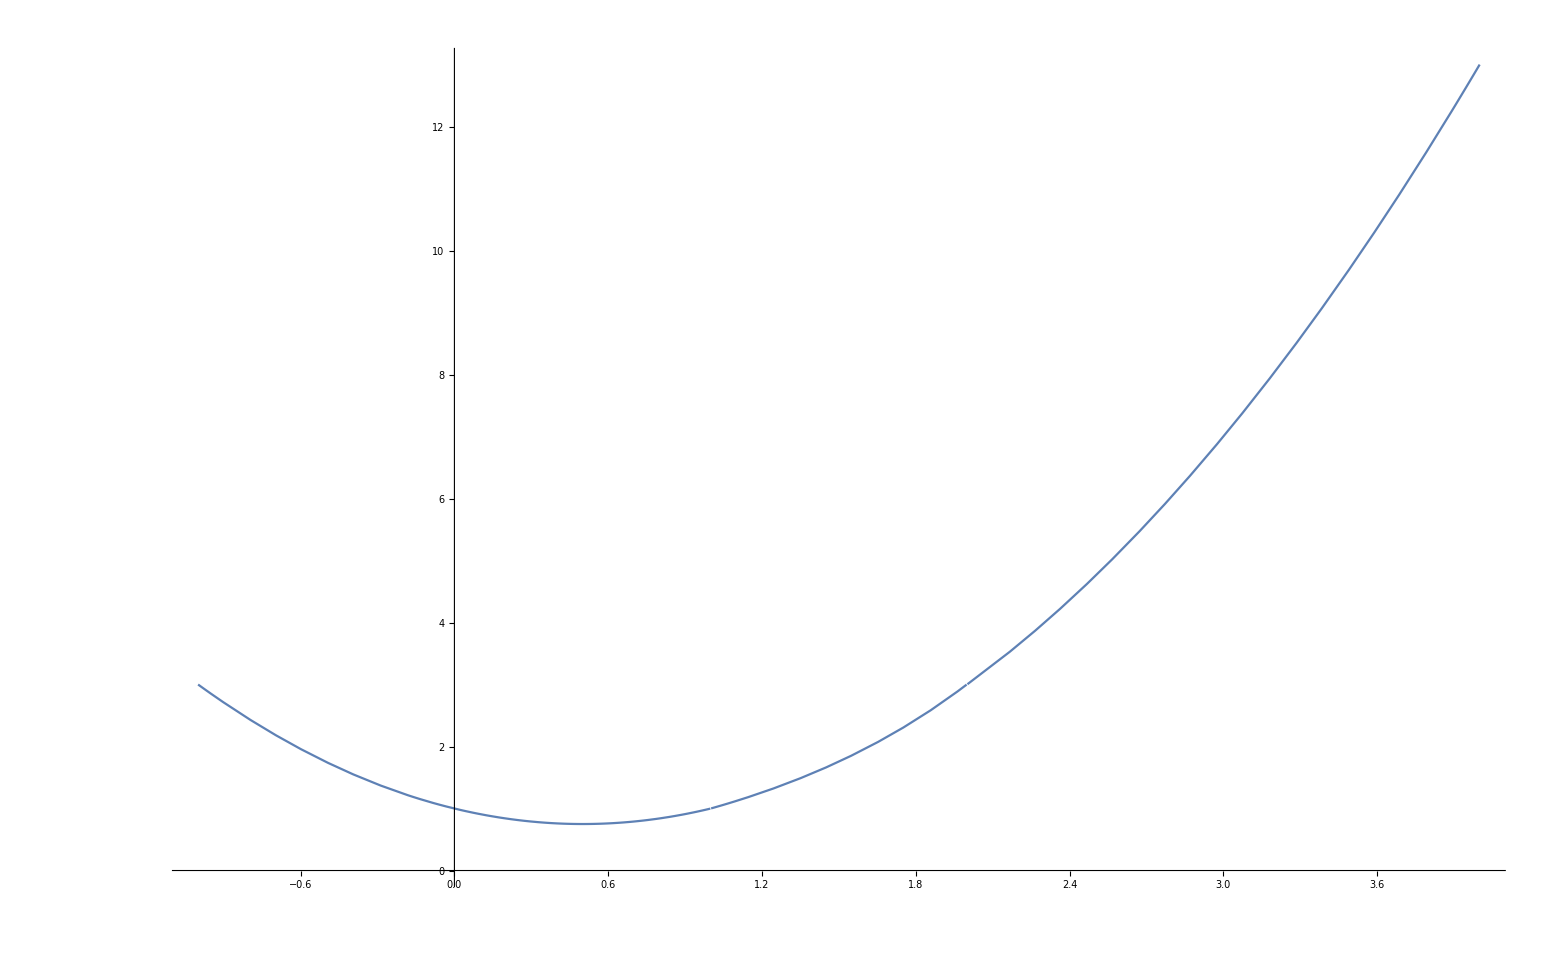

```mathematica
f[x_]:=If[x≤1,Power[x,2]-x+1,If[x≤2,.429(Exp[x]-E)+1,Power[x,2]-x+1]];Plot[f[x],{x,-1,4}]
```

```mathematica
v=.8;e = ParametricPlot3D[{t+1.5,t+1.5,Power[v*t,3]+v*t+1.5},{t,-1.5,1.5}];Show[p,e]
```

-Graphics3D-

```mathematica
Show[%13,ImageSize->Large,ViewPoint->{1.3, -2.4, 2.}]
```

-Graphics3D-

```mathematica
Roots[Power[x,2]-3x+2==0,x]
```

x==1||x==2

```mathematica
ParametricPlot3D[{t+1.5,t+1.5,Power[v*t,3]+v*t+1.5},{t,-1.5,1.5}];Show[p,e]
```

```mathematica
n:=10;For[i=1,i≤n,i++,Export["fun_non_jet_rot"<>ToString[i]<>".png",Show[e,p,ImageSize->Large,ViewPoint->RotationTransform[2*i*Pi/n,{0,0,1}][{3,5,2}],AxesLabel->{"x","f(x)","f'(x)"},Ticks-> None,LabelStyle->Larger],"png"]]
```